# Report Project X

Course code: XXnnnn
Date: 20yy-mm-dd

Name 1, name1@kth.se
Name 2, name2@kth.se

Task 1: Road Construction

## Summery

### Task

The following data illustrates the reference heights along a 2000m long section of a piece of land, where a straight level road shall be built. The heights are given in meters for 200m intervals in x direction. The road width is set to 10m. Your task is to estimate the total volume of the soil mass to be carried away. Suppose the cross section area that the road occupies is a trapezoid height h and with parallel sides 10 and 2h+10+2h.

```mathematica
{0,2.6,5.1,6.3,4.3,2.6,1.3,1.7,2.8,1.5,0}
```

### Result

Let h(x) give the height as a function of distance x. The cross section area can be described as a function of height

A(h)=(10+2h) h

The requested volume to be transported away can thus be calculated with the following integral:

V=∫_0^2000 A(h(x))dx

The result is V≈101×10^3 m^3.

## Road Construction

### Model for cross section area

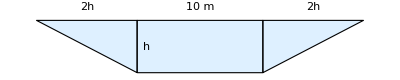

The given trapezoid area is

a(h)=(10+2h)h

x [m] | h [m] | a [m^2]
0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

The data is interpolated as a function A(x).

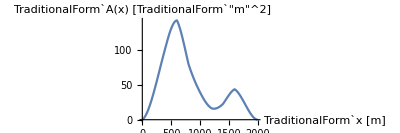

### Model for volume

The requested volume to be transported can be calculated numerically with the integral

V=∫_0^2000 A(x)dx

V≈101×10^3 m^3

I.e. about 0.1 km^3 must be transported.

## Code

```mathematica
ClearAll["`*"]
```

Enter given data

```mathematica
𝕙={0,2.6,5.1,6.3,4.3,2.6,1.3,1.7,2.8,1.5,0};
𝕩=Range[0,2000,200];
```

The cross section area is defined as a function of the height.

```mathematica
a0[h_]:=(10+2h)h
```

A table for a(x) is created by:

```mathematica
data=Transpose[{𝕩,a0[𝕙]}]
```

```mathematica
TableForm[Transpose[{𝕩,𝕙,a0[𝕙]}],TableHeadings->{None,{"x [m]","h [m]","a [m^2]"}}]
```

The function a(x) can now be interpolated:

```mathematica
a=Interpolation[data]
```

```mathematica
Plot[a[x],{x,0,2000},AxesLabel->{x,A},AspectRatio->1/3]
```

Finally, the requested volume is computed

```mathematica
NIntegrate[a[x],{x,0,2000}]
```

Task 2: Kick Length

## Summery

### Task

A certain football path can be described by the following differential equations.

{m x''(t)=-μ x'(t) Abs[x'(t)]
m y''(t)=-m g-μ y'(t)Abs[y'(t)]

In this case, the friction force is proportional to the square of the speed v^2 and opposite to the velocity v⃗. Determine the kick angle toward the ground which gives the greatest kick length. Assume the following data:

m=0.4kg, μ=0.01 kg/m, g=9.8m/s^2

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

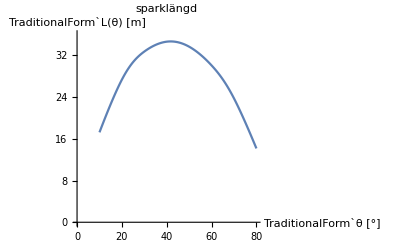

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

```mathematica
ClearAll["`*"]
```

Enter given data.

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Define differential equations and there initial conditions.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Solve the DE.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Example for θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

The curve for different angles.

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

The function for kick length.

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Example

```mathematica
len[45°]
```

A table for different angles.

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Higher accuracy around the max value.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Now, search for the maximum.

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```